```mathematica
d = 1.;
sep = 1.;
a = 1.;

CthMin = 1./2000000.;
CthMax = 2./1.;
nCth = 50;

Cths =CthMin Table[(CthMax/CthMin)^((i-1)/(nCth-1)),{i,1,nCth}];

CthMinEmb = 1./20000.;
CthMaxEmb = 200./1.;
CthsEmb =CthMinEmb Table[(CthMaxEmb/CthMinEmb)^((i-1)/(nCth-1)),{i,1,nCth}];

vMFs12=(2a)/(Pi sep CthsEmb);
vMFs22=Sqrt[(d a)/(sep^2 Cths)];
vMFs23=(2a)/(Pi sep CthsEmb);
vMFs33=Sqrt[(d a)/(sep^3 Cths)];

nVs = 75;
divisor = 3;
multiplier = 1/10;
vMin12 = Min[vMFs12/divisor];
vMax12 = Max[vMFs12 multiplier];
vMin22 = Min[vMFs22/divisor];
vMax22 = Max[vMFs22 multiplier];
vMin23 = Min[vMFs23/divisor];
vMax23 = Max[vMFs23 multiplier];
vMin33 = Min[vMFs33/divisor];
vMax33 = Max[vMFs33 multiplier];

vs12 = vMin12 Table[(vMax12/vMin12)^((i-1)/(nVs-1)),{i,1,nVs}];
vs22 = vMin22 Table[(vMax22/vMin22)^((i-1)/(nVs-1)),{i,1,nVs}];
vs23 = vMin23 Table[(vMax23/vMin23)^((i-1)/(nVs-1)),{i,1,nVs}];
vs33 = vMin33 Table[(vMax33/vMin33)^((i-1)/(nVs-1)),{i,1,nVs}];

nTermsMax = 0.;
nTermsFloor = 50.;
nTerms = Ceiling[nTermsFloor+nTermsMax Min[vs22]/vs22];

nTermsMaxEmb = 15000.;
nTermsFloorEmb = 20.;
nTermsEmb = Ceiling[nTermsFloorEmb+nTermsMaxEmb Min[vs12]/vs12];
```

```mathematica
Cths12 = Table[Sum[Gamma[0,(j sep vs12[[i]])/(4 d)]/(2 Pi d),{j,1,nTermsEmb[[i]]}],{i,1,nVs}];
```

General::munfl: Exp[-721.827] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-761.617] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-801.405] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Cths22 = Table[Sum[Gamma[0,(sep vs22[[i]])/(4 d)(k^2+j^2)/j]/(4 Pi d),{j,1,nTerms[[i]]},{k,-nTerms[[i]]/2,nTerms[[i]]/2}],{i,1,nVs}];
```

General::munfl: Exp[-766.73] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.71388×10^-308 0.0795775 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Timing[Cths23 = Table[Sum[Erfc[Sqrt[(sep vs23[[i]])/(4 d)(k^2+j^2)/j]]/(Pi d sep Sqrt[k^2+j^2]),{j,1,nTermsEmb[[i]]},{k,1, nTermsEmb[[i]]/2}]+Sum[Erfc[Sqrt[(sep vs23[[i]])/(4 d)j]]/(2 Pi d sep j),{j,1,nTermsEmb[[i]]}],{i,1,nVs}];]
```

General::munfl: 9.9603×10^-305 0.000196488 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.21348×10^-305 0.000196366 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.78147×10^-305 0.000196245 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4736.31,Null}

```mathematica
Cths33 = Table[Sum[Erfc[Sqrt[(sep vs33[[i]])/(4 d)(k^2+l^2+j^2)/j]]/(4 Pi d sep Sqrt[k^2+j^2+l^2]),{j,1,nTerms[[i]]},{l,-nTerms[[i]]/2, nTerms[[i]]/2},{k,-nTerms[[i]]/2,nTerms[[i]]/2}],{i,1,nVs}];
```

General::munfl: 2.05972×10^-307 0.00234153 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.95579×10^-307 0.00234356 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

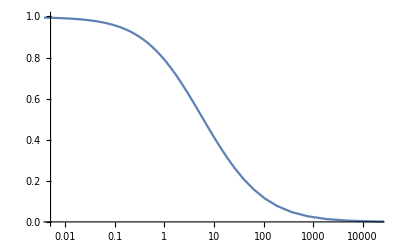

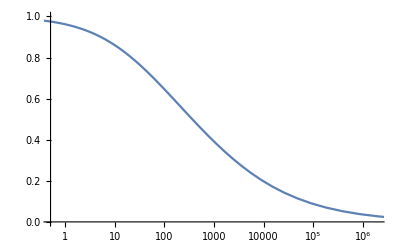

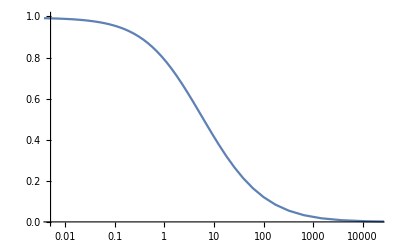

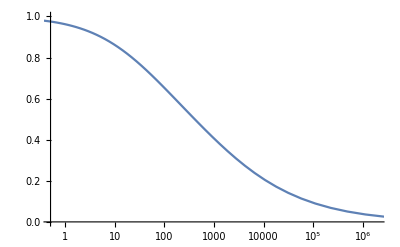

```mathematica
ListLogLinearPlot[Transpose[{1/Cths12,vs12/(2/Cths12/sep/Pi)}],PlotRange->{{1/CthMaxEmb,1/CthMinEmb},{0,1}},Joined->True]
ListLogLinearPlot[Transpose[{1/Cths22,vs22/Sqrt[d/Cths22/sep^2]}],PlotRange->{{1/CthMax,1/CthMin},{0,1}},Joined->True]
ListLogLinearPlot[Transpose[{1/Cths23,vs23/(2/Cths23/sep^2/Pi)}],PlotRange->{{1/CthMaxEmb,1/CthMinEmb},{0,1}},Joined->True]
ListLogLinearPlot[Transpose[{1/Cths33,vs33/Sqrt[d/Cths33/sep^2]}],PlotRange->{{1/CthMax,1/CthMin},{0,1}}, Joined->True]
```

```mathematica
Transpose[{Cths12,vs12}]
Transpose[{Cths22,vs22}]
Transpose[{Cths23,vs23}]
Transpose[{Cths33,vs33}]

func12 = Interpolation[Transpose[{Cths12,vs12/(2/Cths12/sep/Pi)}],InterpolationOrder->1];
func22 = Interpolation[Transpose[{Cths22,vs22/Sqrt[d/Cths22/sep^2]}],InterpolationOrder->1];
func23 = Interpolation[Transpose[{Cths23,vs23/(2/Cths23/sep^2/Pi)}],InterpolationOrder->1];
func33 = Interpolation[Transpose[{Cths33,vs33/Sqrt[d/Cths33/sep^2]}],InterpolationOrder->1];
```

{{597.29,0.00106103},{494.236,0.00128198},{408.947,0.00154893},{338.359,0.00187147},{279.939,0.00226117},{231.59,0.00273202},{191.576,0.00330092},{158.461,0.00398829},{131.056,0.00481879},{108.377,0.00582222},{89.6091,0.00703461},{74.0782,0.00849945},{61.2264,0.0102693},{50.5923,0.0124078},{41.7936,0.0149915},{34.5137,0.0181132},{28.4913,0.021885},{23.5089,0.0264422},{19.3883,0.0319484},{15.98,0.0386011},{13.1617,0.0466392},{10.8316,0.056351},{8.90541,0.0680852},{7.3139,0.0822629},{5.99914,0.0993929},{4.91318,0.12009},{4.01688,0.145097},{3.27748,0.175311},{2.66804,0.211816},{2.16592,0.255924},{1.75273,0.309216},{1.41318,0.373605},{1.13459,0.451403},{0.906427,0.5454},{0.720012,0.658971},{0.568142,0.796191},{0.444859,0.961985},{0.345199,1.1623},{0.265055,1.40433},{0.201012,1.69676},{0.150234,2.05009},{0.11036,2.47699},{0.0794208,2.99278},{0.0557694,3.61598},{0.0380235,4.36895},{0.0250174,5.27872},{0.0157635,6.37792},{0.00942214,7.70603},{0.00527934,9.31068},{0.00273236,11.2495},{0.0012827,13.592},{0.000534206,16.4223},{0.000192156,19.842},{0.0000578179,23.9738},{0.0000140086,28.966},{2.61193×10^-6,34.9977},{3.54972×10^-7,42.2854},{3.29412×10^-8,51.0907},{1.92921×10^-9,61.7295},{6.48278×10^-11,74.5837},{1.11402×10^-12,90.1145},{8.5181×10^-15,108.879},{2.44947×10^-17,131.552},{2.16176×10^-20,158.945},{4.58001×10^-24,192.043},{1.73116×10^-28,232.033},{8.15532×10^-34,280.351},{3.10419×10^-40,338.729},{5.65483×10^-48,409.264},{2.61843×10^-57,494.487},{1.43471×10^-68,597.456},{3.69308×10^-82,721.866},{1.46272×10^-98,872.184},{2.3141×10^-118,1053.8},{2.86672×10^-142,1273.24}}

{{16.6119,0.235702},{14.1941,0.256984},{12.0861,0.280188},{10.2591,0.305486},{8.68434,0.333069},{7.33378,0.363142},{6.18075,0.395931},{5.20022,0.43168},{4.36913,0.470657},{3.66662,0.513153},{3.07407,0.559486},{2.57508,0.610003},{2.15539,0.665081},{1.80274,0.725132},{1.50661,0.790606},{1.25808,0.861991},{1.04961,0.939821},{0.874819,1.02468},{0.72834,1.1172},{0.605653,1.21807},{0.502955,1.32805},{0.417047,1.44796},{0.345241,1.5787},{0.285274,1.72125},{0.235243,1.87666},{0.19355,2.04611},{0.158849,2.23085},{0.130011,2.43228},{0.106084,2.65189},{0.0862695,2.89134},{0.0698962,3.1524},{0.0563995,3.43703},{0.0453047,3.74737},{0.0362132,4.08572},{0.0287899,4.45463},{0.0227532,4.85684},{0.0178662,5.29538},{0.01393,5.7735},{0.0107776,6.2948},{0.00826862,6.86317},{0.00628538,7.48285},{0.00472955,8.15849},{0.00351912,8.89513},{0.00258602,9.69828},{0.00187403,10.574},{0.00133699,11.5287},{0.000937207,12.5696},{0.000644054,13.7046},{0.000432813,14.942},{0.000283639,16.2911},{0.000180719,17.762},{0.000111584,19.3658},{0.0000665345,21.1144},{0.0000381704,23.0208},{0.000020986,25.0994},{0.0000110113,27.3657},{5.48917×10^-6,29.8365},{2.58738×10^-6,32.5305},{1.14727×10^-6,35.4678},{4.75891×10^-7,38.6702},{1.83558×10^-7,42.1618},{6.54077×10^-8,45.9686},{2.13788×10^-8,50.1192},{6.36028×10^-9,54.6445},{1.70781×10^-9,59.5784},{4.10091×10^-10,64.9579},{8.71842×10^-11,70.823},{1.62316×10^-11,77.2177},{2.61496×10^-12,84.1898},{3.59833×10^-13,91.7914},{4.16968×10^-14,100.079},{4.00636×10^-15,109.116},{3.13845×10^-16,118.968},{1.96791×10^-17,129.71},{9.68068×10^-19,141.421}}

{{595.66,0.00106103},{492.889,0.00128198},{407.834,0.00154893},{337.439,0.00187147},{279.179,0.00226117},{230.964,0.00273202},{191.06,0.00330092},{158.035,0.00398829},{130.705,0.00481879},{108.089,0.00582222},{89.372,0.00703461},{73.8837,0.00849945},{61.0675,0.0102693},{50.4621,0.0124078},{41.688,0.0149915},{34.4276,0.0181132},{28.4223,0.021885},{23.4532,0.0264422},{19.3436,0.0319484},{15.9445,0.0386011},{13.1342,0.0466392},{10.8098,0.056351},{8.88894,0.0680852},{7.30159,0.0822629},{5.98989,0.0993929},{4.90645,0.12009},{4.01241,0.145097},{3.27435,0.175311},{2.66637,0.211816},{2.16496,0.255924},{1.75243,0.309216},{1.4132,0.373605},{1.13492,0.451403},{0.906894,0.5454},{0.720537,0.658971},{0.568705,0.796191},{0.445436,0.961985},{0.345783,1.1623},{0.26564,1.40433},{0.201597,1.69676},{0.150819,2.05009},{0.110945,2.47699},{0.0800059,2.99278},{0.0563543,3.61598},{0.0386071,4.36895},{0.0255959,5.27872},{0.0163258,6.37792},{0.00994666,7.70603},{0.00573527,9.31068},{0.00309037,11.2495},{0.00152919,13.592},{0.000678949,16.4223},{0.00026272,19.842},{0.0000855723,23.9738},{0.0000225322,28.966},{4.57645×10^-6,34.9977},{6.78538×10^-7,42.2854},{6.87729×10^-8,51.0907},{4.40308×10^-9,61.7295},{1.61876×10^-10,74.5837},{3.04554×10^-12,90.1145},{2.5511×10^-14,108.879},{8.04078×10^-17,131.552},{7.78158×10^-20,158.945},{1.80855×10^-23,192.043},{7.50142×10^-28,232.033},{3.87892×10^-33,280.351},{1.621×10^-39,338.729},{3.24268×10^-47,409.264},{1.6491×10^-56,494.487},{9.92543×10^-68,597.456},{2.80675×10^-81,721.866},{1.22137×10^-97,872.184},{2.12313×10^-117,1053.8},{2.8901×10^-141,1273.24}}

{{16.254,0.235702},{13.9579,0.256984},{11.9348,0.280188},{10.1651,0.305486},{8.62789,0.333069},{7.30115,0.363142},{6.16267,0.395931},{5.19069,0.43168},{4.36441,0.470657},{3.66449,0.513153},{3.07326,0.559486},{2.57491,0.610003},{2.15552,0.665081},{1.80299,0.725132},{1.50691,0.790606},{1.2584,0.861991},{1.04994,0.939821},{0.875147,1.02468},{0.728669,1.1172},{0.605982,1.21807},{0.503284,1.32805},{0.417377,1.44796},{0.345571,1.5787},{0.285603,1.72125},{0.235572,1.87666},{0.193879,2.04611},{0.159179,2.23085},{0.13034,2.43228},{0.106413,2.65189},{0.0865989,2.89134},{0.0702256,3.1524},{0.0567288,3.43703},{0.0456338,3.74737},{0.036542,4.08572},{0.0291179,4.45463},{0.0230796,4.85684},{0.0181901,5.29538},{0.0142498,5.7735},{0.011091,6.2948},{0.00857288,6.86317},{0.00657722,7.48285},{0.00500535,8.15849},{0.00377523,8.89513},{0.00281909,9.69828},{0.00208138,10.574},{0.00151686,11.5287},{0.00108899,12.5696},{0.000768358,13.7046},{0.000531366,14.942},{0.000359098,16.2911},{0.000236372,17.762},{0.000151014,19.3658},{0.0000932931,21.1144},{0.0000555112,23.0208},{0.0000316817,25.0994},{0.0000172679,27.3657},{8.9468×10^-6,29.8365},{4.38501×10^-6,32.5305},{2.02245×10^-6,35.4678},{8.72877×10^-7,38.6702},{3.50401×10^-7,42.1618},{1.29976×10^-7,45.9686},{4.4234×10^-8,50.1192},{1.37047×10^-8,54.6445},{3.83295×10^-9,59.5784},{9.58843×10^-10,64.9579},{2.12397×10^-10,70.823},{4.1208×10^-11,77.2177},{6.91923×10^-12,84.1898},{9.92481×10^-13,91.7914},{1.19897×10^-13,100.079},{1.20113×10^-14,109.116},{9.81153×10^-16,118.968},{6.41583×10^-17,129.71},{3.2917×10^-18,141.421}}

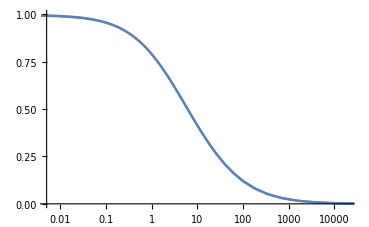

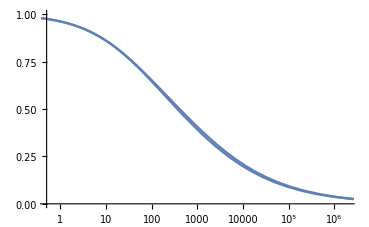

```mathematica
Show[ListLogLinearPlot[Transpose[{1/Cths12,vs12/(2/Cths12/sep/Pi)}],PlotRange->{{1/CthMaxEmb,1/CthMinEmb},{0,1}},Joined->True],ListLogLinearPlot[Transpose[{1/Cths23,vs23/(2/Cths23/sep^2/Pi)}],PlotRange->{{1/CthMaxEmb,1/CthMinEmb},{0,1}},Joined->True]]
Show[ListLogLinearPlot[Transpose[{1/Cths22,vs22/Sqrt[d/Cths22/sep^2]}],PlotRange->{{1/CthMax,1/CthMin},{0,1}},Joined->True],
ListLogLinearPlot[Transpose[{1/Cths33,vs33/Sqrt[d/Cths33/sep^2]}],PlotRange->{{1/CthMax,1/CthMin},{0,1}}, Joined->True]]
```

```mathematica
Cth11 = {100., 10., 1., 0.1, 0.01, 0.001, 0.0001, 1 10^-5, 1 10^-6,30., 3., 0.3, 0.03, 0.003, 0.0003, 3 10^-5, 3 10^-6};
Cth12 = {0.0001,0.01,0.001,1.,100.,0.1,10.,30.,3.,0.3,0.03,0.003,0.0003};
Cth22 = {0.01,0.001, 1. 10^-5,0.1,0.0001,1 10^-6,1., 0.3, 0.03, 0.003, 0.0003, 3 10^-5, 3 10^-6};
Cth23 ={0.01,0.1,10.,0.0001,0.001,1.,3.,0.3,0.03,0.003,0.0003};
Cth33 = {0.1,1.,1. 10^-6,0.0001,0.01,0.001, 1 10^-5, 0.3, 0.03, 0.003, 0.0003, 3 10^-5, 3 10^-6};

vMult11 ={0.9708649081754902,0.9493730675162828,0.8780489236338908,0.6923180123275964,0.44327726281101476,0.23277638443097515,0.10831437148017707,0.04371807034944297,0.018219297259383187,0.9570270672913624,0.9186959033920918,0.7730854270227239,0.5541178956588995,0.3236964976984738,0.16112705524438084,0.07123214236189325,0.02896126990919698};
vMult12 = {0.0017467035548579745,0.06595858492449354,0.011825742051655928,0.6006292871299392,0.9732648558583583,0.2537815240714069,0.8841751356712579,0.9515026221625402,0.7840554737761767,0.4305862279500584,0.1348249559078189,0.02762587191503333,0.004430873458316804};
vMult22 = {0.6759599769759534,0.3828710718303534,0.08274555114419763,0.8809537842876083,0.19575513953088705,0.03318709580438012,0.9765146155673102,0.9331744218570176,0.8009286633265763,0.5438868506574708,0.2709228926202728,0.12367684785845556,0.05481206580034799};
vMult23 = {0.12073058590281423,0.43224057940639893,0.964565735902969,0.0035081510035321153,0.024091558352406478,0.8291373059468805,0.9274473726546824,0.6365075942814681,0.23877230172932895,0.0546135706129886,0.00893176275669686};
vMult33 = {0.9239334838235415,0.9789494994362247,0.03683258760137096,0.21428110900971753,0.7038148603695958,0.43443196036147197,0.09468158370260663,0.9601749365780649,0.8358509115497492,0.5642339320499635,0.2934113060754763,0.13105374454273264,0.05685274905676026};

d12 = {1./30.,1./10.,1./3.,1.,3.,10.,30.};
d22 = {1./30.,1./10.,1./3.,1.,3.,10.,30.};

vMult12d = {0.25220991116165126,0.2667690478229536,0.2625614033833103,0.2612531329394698,0.255606017087181,0.26006275297034925,0.25269402338318436};
vMult22d = {0.37065195978692633,0.3831378606707667,0.38877673118591305,0.38107106141287667,0.38237657485118304,0.3802398853377577,0.39841721133655017};
```

```mathematica
int11 = Interpolation[Transpose[{Cth11,vMult11}],InterpolationOrder->1];
int12 = Interpolation[Transpose[{Cth12,vMult12}],InterpolationOrder->1];
int22 = Interpolation[Transpose[{Cth22,vMult22}],InterpolationOrder->1];
int23 = Interpolation[Transpose[{Cth23,vMult23}],InterpolationOrder->1];
int33 = Interpolation[Transpose[{Cth33,vMult33}],InterpolationOrder->1];
```

```mathematica
int33[1.]
```

0.978949

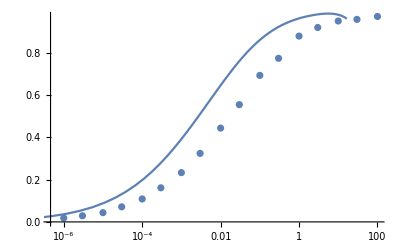

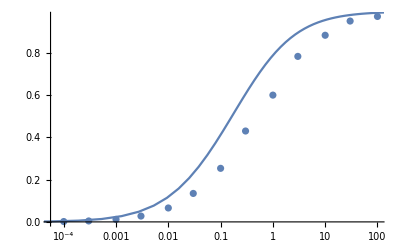

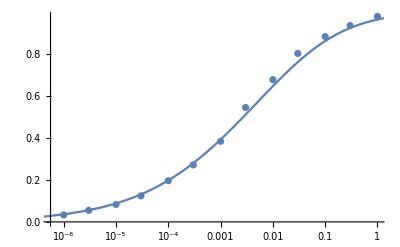

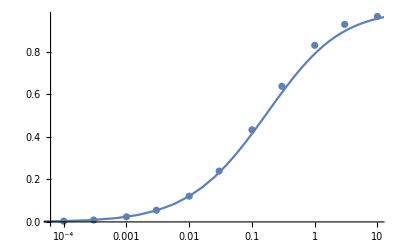

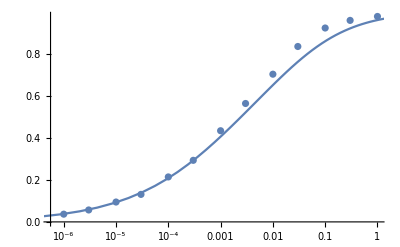

```mathematica
Show[ListLogLinearPlot[Transpose[{Cth11,vMult11}]],ListLogLinearPlot[Transpose[{Cths22,vs22/Sqrt[d/Cths22/sep^2]}],Joined->True]]
Show[ListLogLinearPlot[Transpose[{Cth12,vMult12}]],ListLogLinearPlot[Transpose[{Cths12,vs12/(2/Cths12/sep/Pi)}],Joined->True]]
Show[ListLogLinearPlot[Transpose[{Cth22,vMult22}]],ListLogLinearPlot[Transpose[{Cths22,vs22/Sqrt[d/Cths22/sep^2]}],Joined->True]]
Show[ListLogLinearPlot[Transpose[{Cth23,vMult23}]],ListLogLinearPlot[Transpose[{Cths23,vs23/(2/Cths23/sep^2/Pi)}],Joined->True]]
Show[ListLogLinearPlot[Transpose[{Cth33,vMult33}]],ListLogLinearPlot[Transpose[{Cths33,vs33/Sqrt[d/Cths33/sep^3]}],Joined->True]]
```

```mathematica
plotColor = RGBColor[0., 0., 0.];
dashedColor = RGBColor[0.6,0.6,0.6];

wid = 1600;
hei = 1000;
aR = hei/wid;

wid2 = 1600;
hei2 = 550;
aR2 = hei2/wid2;

wid3 = 1550;
hei3 = 1950;
aR3 = hei3/wid3;

minorThickness = Thickness[20/wid];
majorThickness = Thickness[25/wid];
majorMajorThickness = Thickness[30/wid];
tL = 75/wid;
fS = Directive[Black,minorThickness];
tS = Directive[Black,minorThickness];
markerSize = wid/18;
markerPrefs = Graphics[{plotColor,Thickness[0.15],Circle[]}, ImageSize->markerSize];

pR = {{1/CthMaxEmb,1/CthMinEmb},{0,1}};
pR2 = {{1/CthMax,1/CthMin},{0,1}};
pR3 = {{1/60,60},{0,1.}};
fT = {{{#,"",{tL,0}}&/@{0.5},None},{{#,"",{tL,0}}&/@{0.01,10,10^4},None}};
fT2 = {{{#,"",{tL,0}}&/@{0.5},None},{{#,"",{tL,0}}&/@{1,1000,10^6},None}};
fT3 = {{{#,"",{tL,0}}&/@{0.5},None},{{#,"",{tL,0}}&/@{0.1,1,10},None}};
```

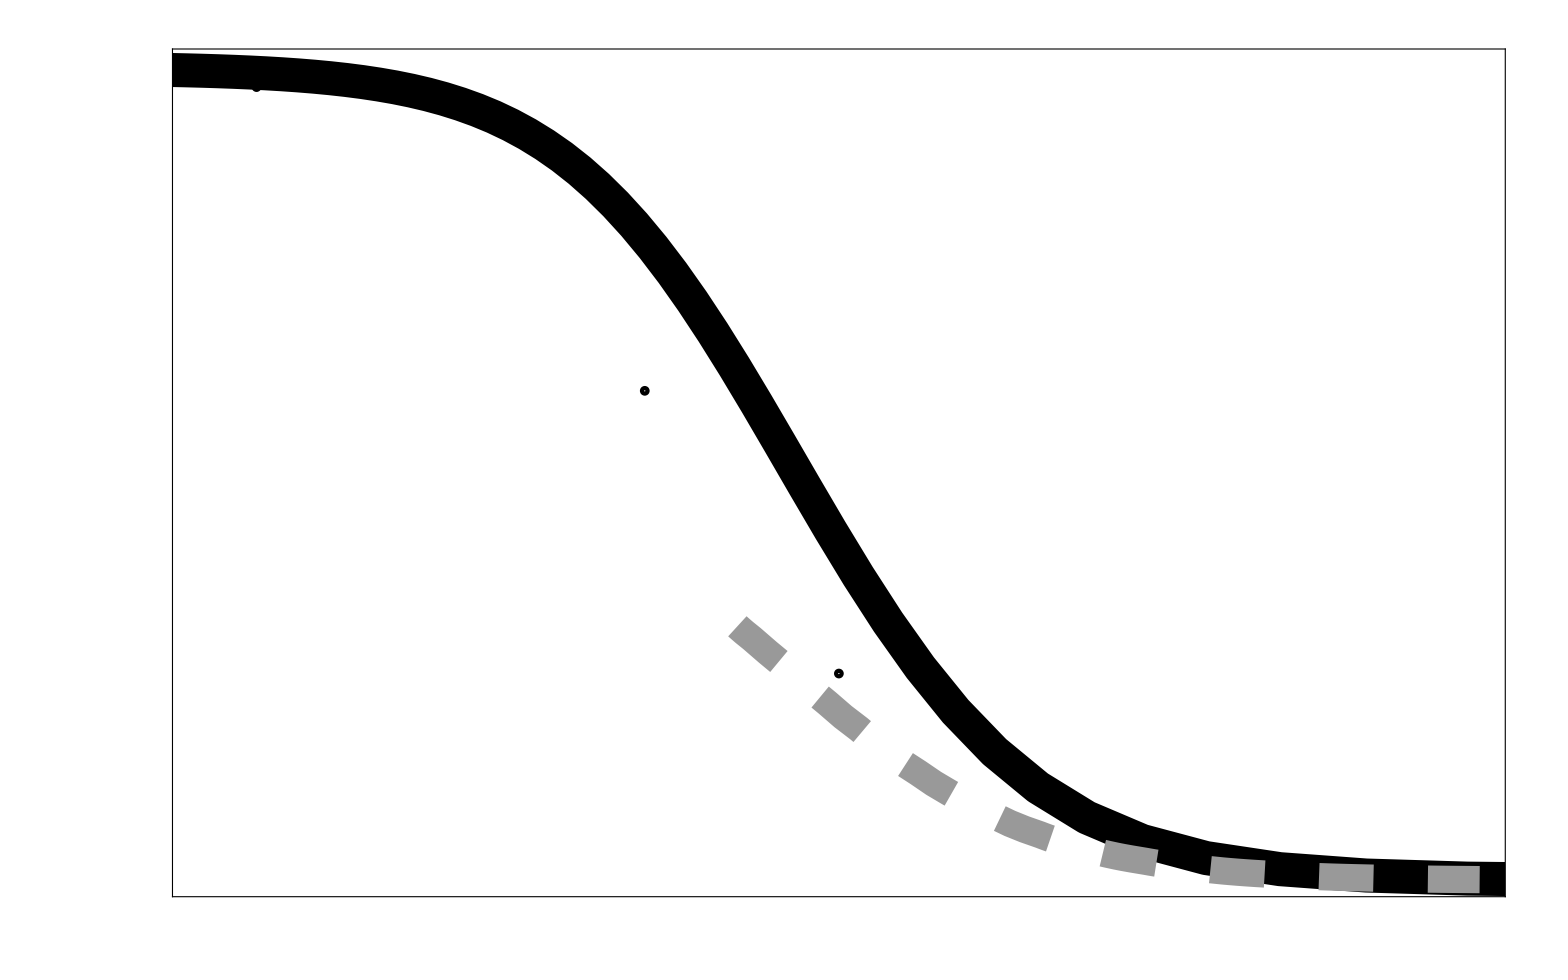

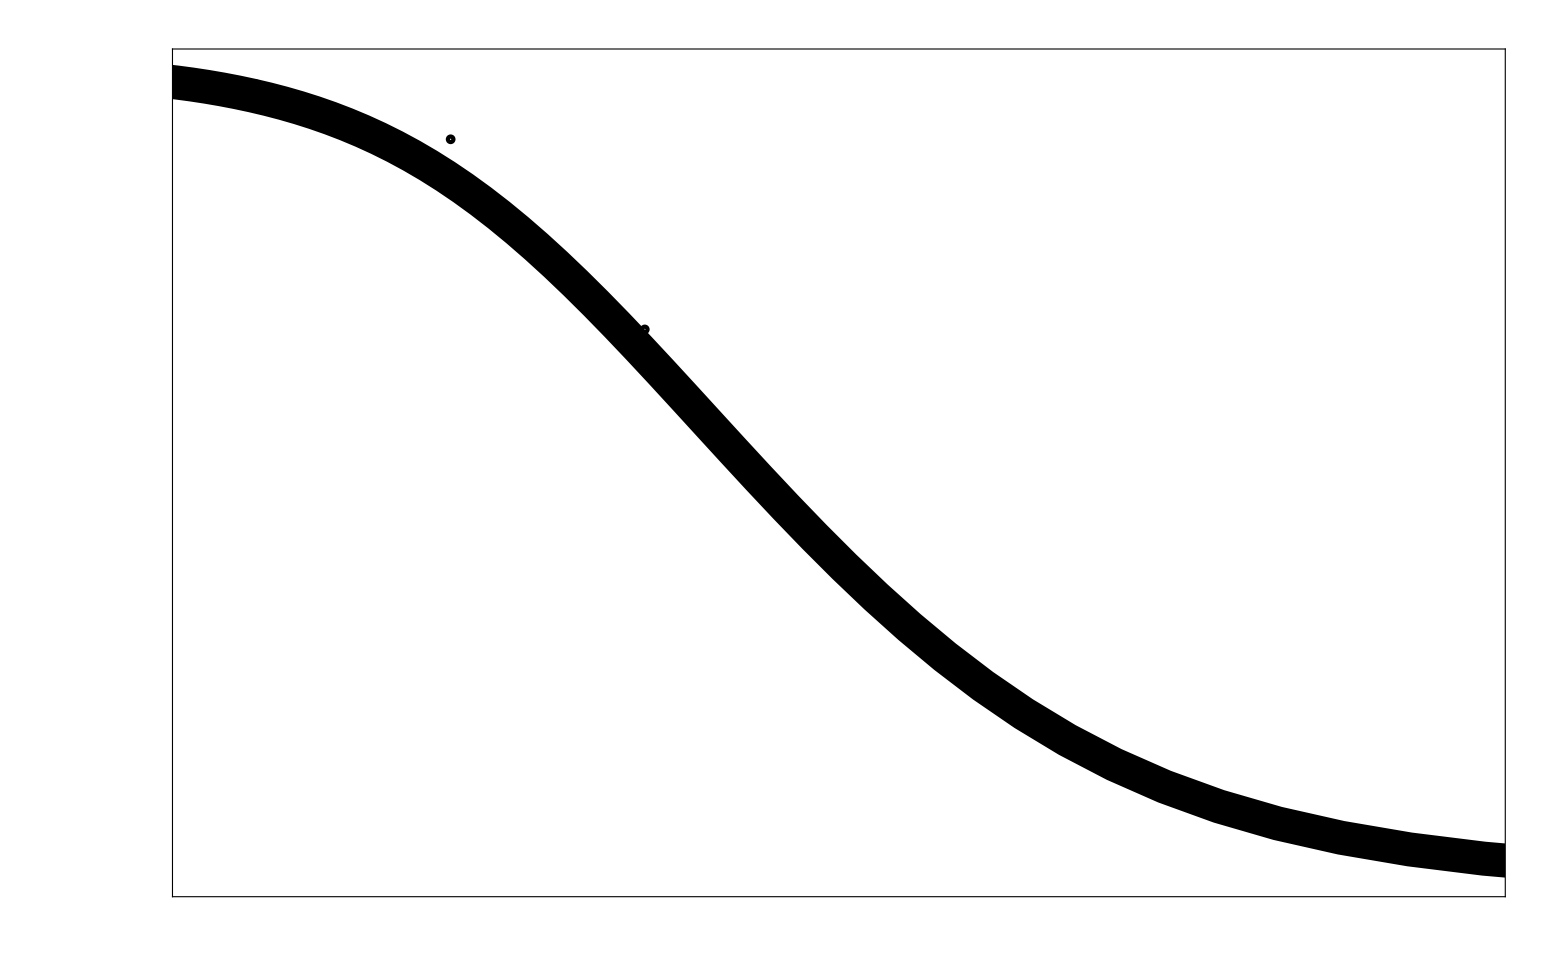

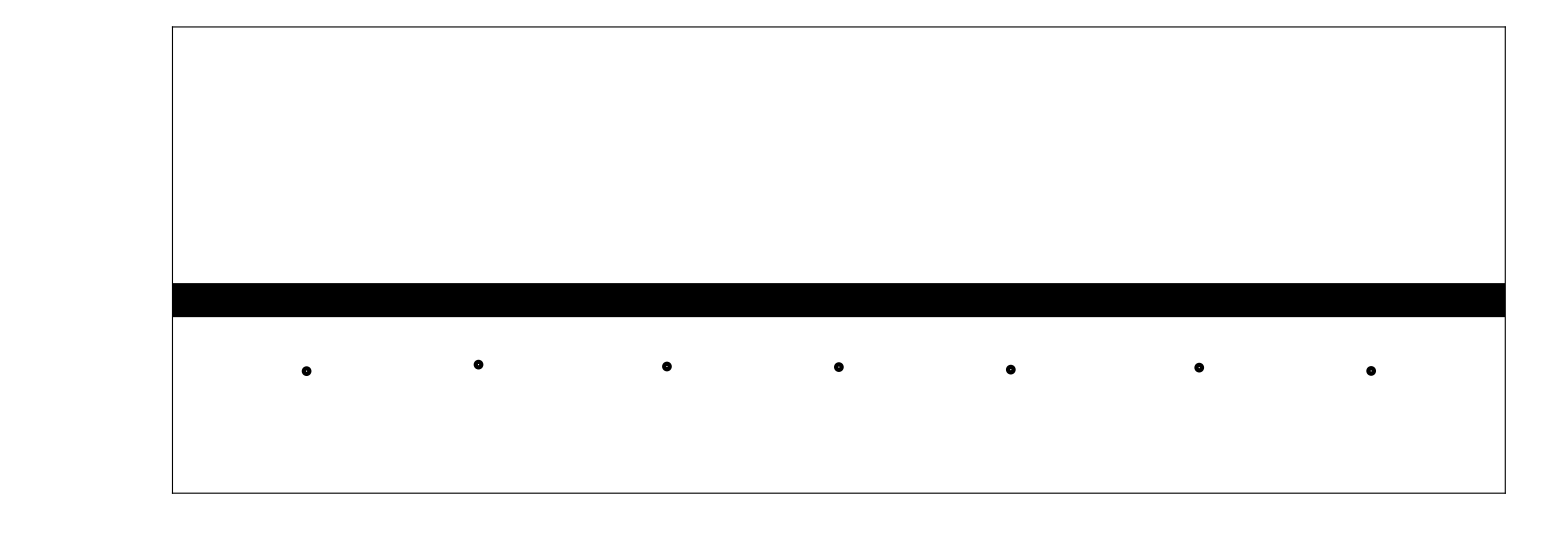

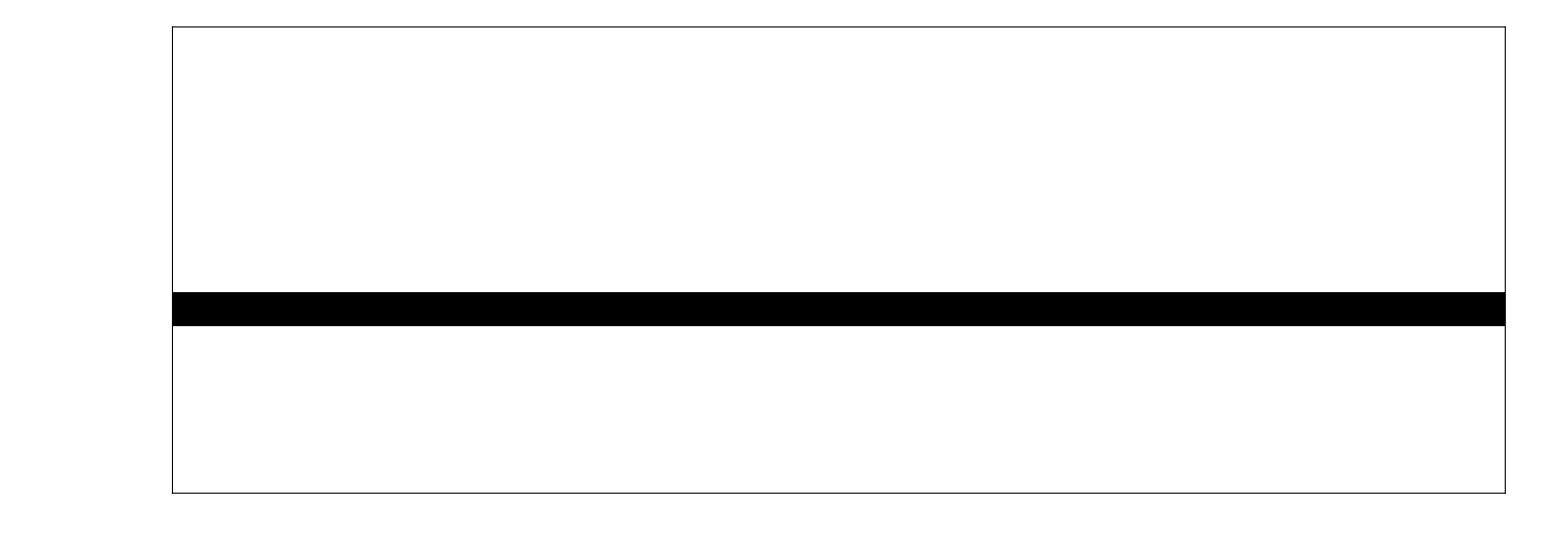

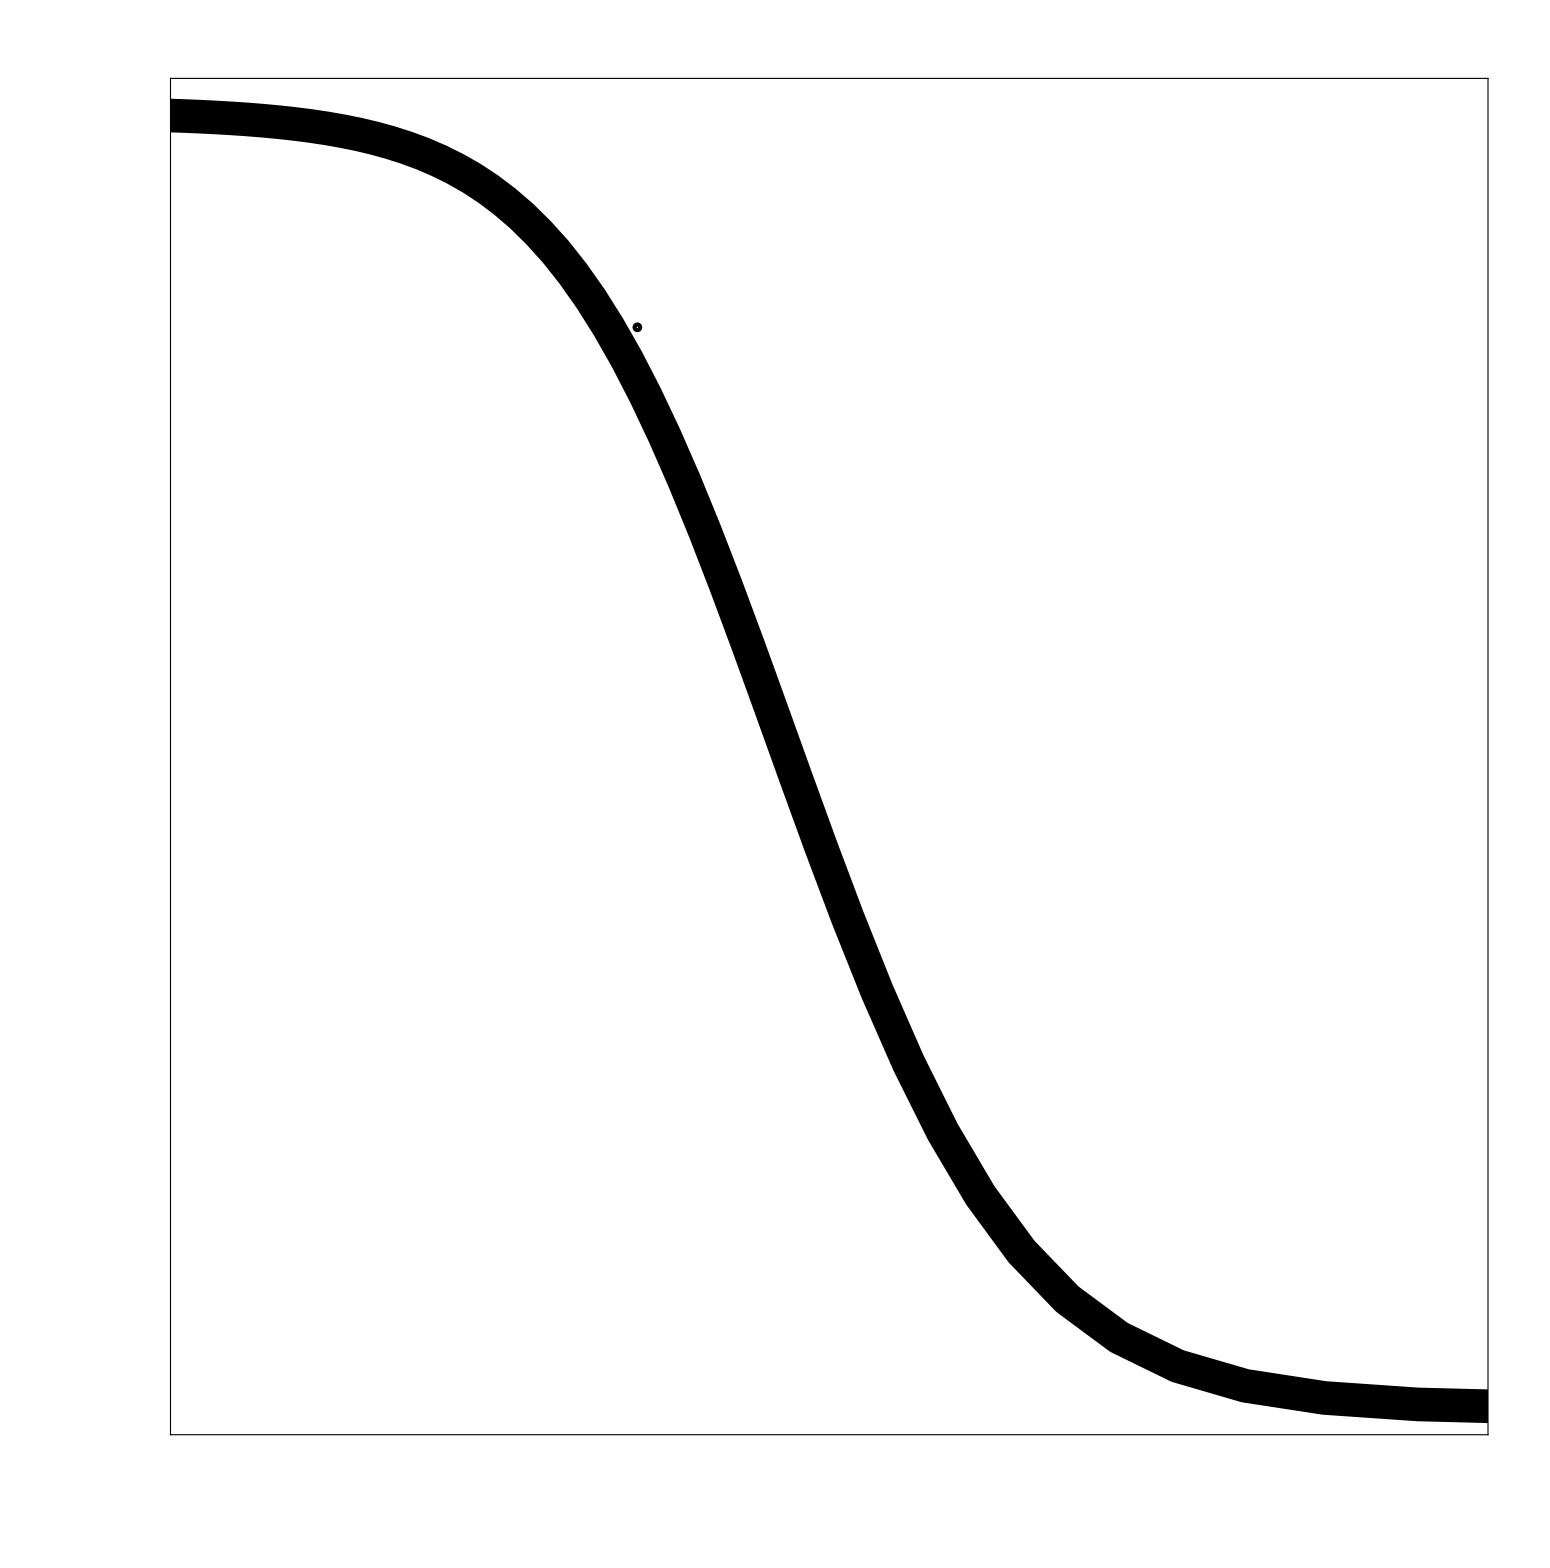

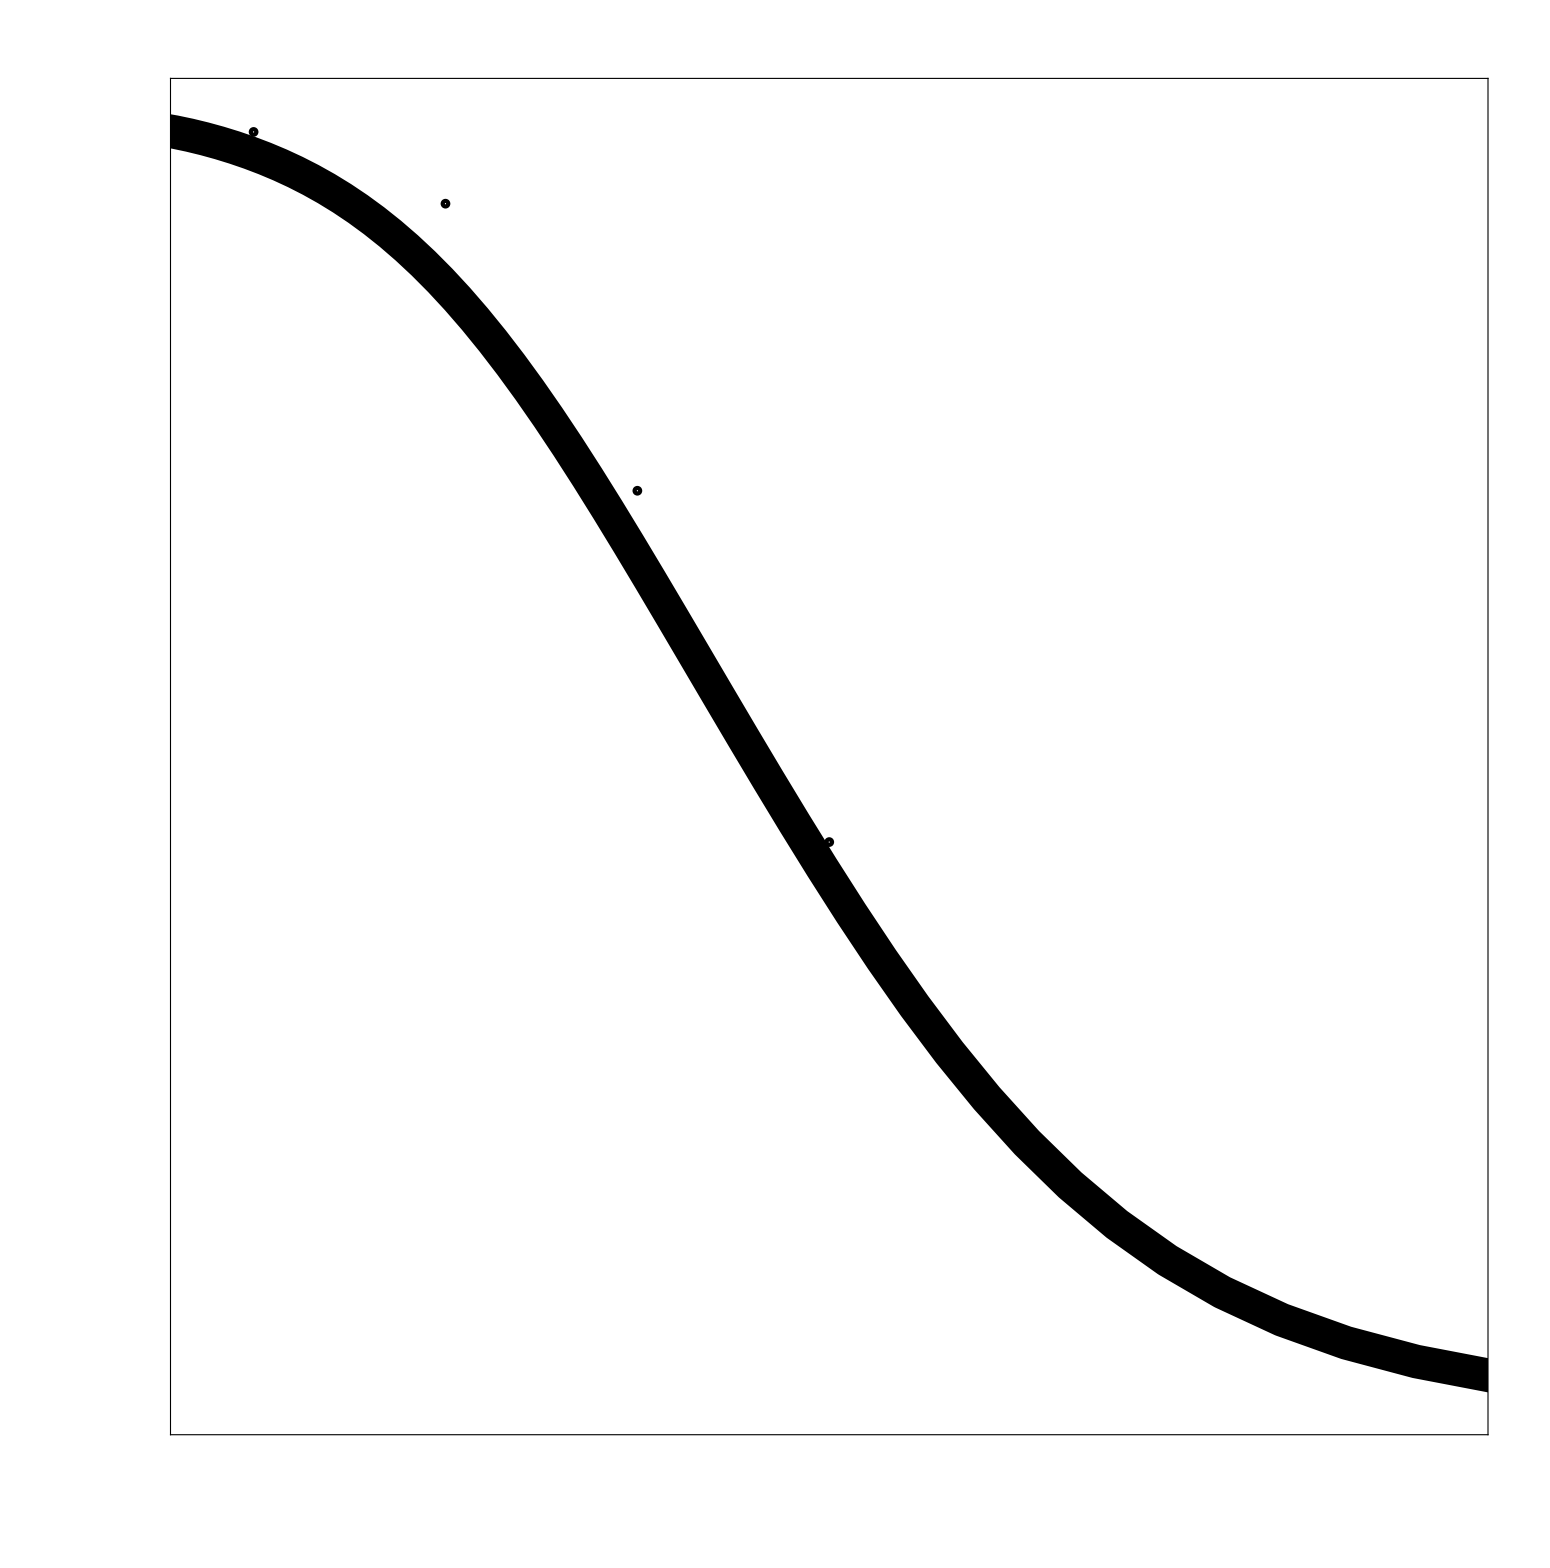

```mathematica
plot12 = Show[ListLogLinearPlot[Transpose[{1/Cth12,vMult12}],PlotRange->pR,Frame->True,FrameStyle->fS,PlotMarkers->markerPrefs,AspectRatio->aR,TicksStyle->tS,FrameTicks->fT],ListLogLinearPlot[Transpose[{1/Cths12,vs12/(2/Cths12/sep/Pi)}],Joined->True,PlotStyle->{majorThickness,plotColor}],LogLinearPlot[func12[1/x]/2,{x,3,1/CthMinEmb},PlotStyle->{minorThickness,dashedColor,Dashing[{0.025,0.025}]}],ImageSize->wid]

plot22 = Show[ListLogLinearPlot[Transpose[{1/Cths22,vs22/Sqrt[d/Cths22/sep^2]}],PlotRange->pR2,Joined->True,Frame->True,FrameStyle->fS,PlotStyle->{majorThickness,plotColor},AspectRatio->aR,TicksStyle->tS,FrameTicks->fT2],ListLogLinearPlot[Transpose[{1/Cth22,vMult22}],PlotMarkers->markerPrefs],ImageSize->wid]

vMult12Plot = func12[0.1];
vMult22Plot = func22[0.001];
plot12d = Show[LogLinearPlot[vMult12Plot,{x,1/100,100},PlotRange->pR3,Frame->True,FrameStyle->fS,PlotStyle->{majorThickness,plotColor},AspectRatio->aR2,TicksStyle->tS,FrameTicks->fT3],ListLogLinearPlot[Transpose[{d12,vMult12d}],PlotMarkers->markerPrefs],ImageSize->wid2]
plot22d = Show[LogLinearPlot[vMult22Plot,{x,1/100,100},PlotRange->pR3,Frame->True,FrameStyle->fS,PlotStyle->{majorThickness,plotColor},AspectRatio->aR2,TicksStyle->tS,FrameTicks->fT3],ListLogLinearPlot[Transpose[{d22,vMult22d}],PlotMarkers->markerPrefs],ImageSize->wid2]

plot23 = Show[ListLogLinearPlot[Transpose[{1/Cths23,vs23/(2/Cths23/sep^2/Pi)}],PlotRange->pR,Joined->True,Frame->True,FrameStyle->fS,PlotStyle->{majorThickness,plotColor},AspectRatio->aR3,TicksStyle->tS,FrameTicks->fT],ListLogLinearPlot[Transpose[{1/Cth23,vMult23}],PlotMarkers->markerPrefs],ImageSize->wid3]

plot33 = Show[ListLogLinearPlot[Transpose[{1/Cths33,vs33/Sqrt[d/Cths33/sep^2]}],PlotRange->pR2,Joined->True,Frame->True,FrameStyle->fS,PlotStyle->{majorThickness,plotColor},AspectRatio->aR3,TicksStyle->tS,FrameTicks->fT2],ListLogLinearPlot[Transpose[{1/Cth33,vMult33}],PlotMarkers->markerPrefs],ImageSize->wid3]
```

```mathematica
Export["plot12.pdf",plot12]
Export["plot12d.pdf",plot12d]
Export["plot22.pdf",plot22]
Export["plot22d.pdf",plot22d]
Export["plot23.pdf",plot23]
Export["plot33.pdf",plot33]
```

plot12.pdf

plot12d.pdf

plot22.pdf

plot22d.pdf

plot23.pdf

plot33.pdf